```mathematica
Clear[Lx,Ly,m0,filename,ChernMatrixSiteWiseList,BinCountTable]
```

```mathematica
(**----------Data analysis of Local Chern Number-----------**)
```

```mathematica
(** m = -1 **)
```

```mathematica
L={20,24,28,32,36,40,44,48,52,56,60}
```

{20,24,28,32,36,40,44,48,52,56,60}

```mathematica
OneOverL = N[Table[1/L[[ii]],{ii,1,Length[L]}]]
```

{0.05,0.0416667,0.0357143,0.03125,0.0277778,0.025,0.0227273,0.0208333,0.0192308,0.0178571,0.0166667}

```mathematica
PercentageDelta0pt1 = {0.56,0.625,0.678571,0.71875,0.709877,0.73,0.75,0.746528,0.752959,0.765306,0.78}
```

{0.56,0.625,0.678571,0.71875,0.709877,0.73,0.75,0.746528,0.752959,0.765306,0.78}

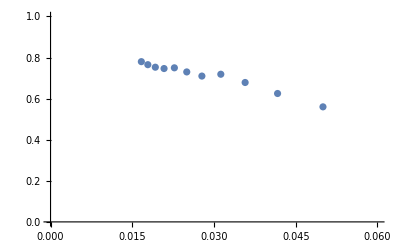

```mathematica
ListPlot[Transpose@{OneOverL,PercentageDelta0pt1},PlotRange->{{0,0.06},{0,1}}]
```

```mathematica
(**-------------------------------------------------------------------------------***)
```

```mathematica
PercentageDelta0pt3 = {0.65,0.694444,0.734694,0.765625,0.790123,0.81,0.826446,0.838542,0.821006,0.832908,0.842222}
```

{0.65,0.694444,0.734694,0.765625,0.790123,0.81,0.826446,0.838542,0.821006,0.832908,0.842222}

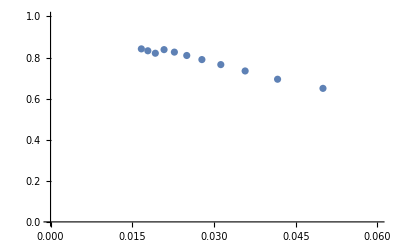

```mathematica
ListPlot[Transpose@{OneOverL,PercentageDelta0pt3},PlotRange->{{0,0.06},{0,1}}]
```

```mathematica
PercentageDelta0pt5 = {0.75,0.777778,0.744898,0.769531,0.79321,0.8125,0.832645,0.840278,0.852071,0.862245,0.871111}
```

{0.75,0.777778,0.744898,0.769531,0.79321,0.8125,0.832645,0.840278,0.852071,0.862245,0.871111}

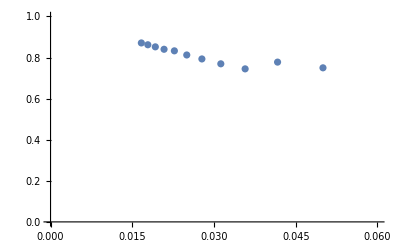

```mathematica
ListPlot[Transpose@{OneOverL,PercentageDelta0pt5},PlotRange->{{0,0.06},{0,1}}]
```

```mathematica
PercentageDelta0pt7 = {0.81,0.791667,0.806122,0.828125,0.845679,0.82,0.836777,0.845486,0.85503,0.864796,0.873333}
```

{0.81,0.791667,0.806122,0.828125,0.845679,0.82,0.836777,0.845486,0.85503,0.864796,0.873333}

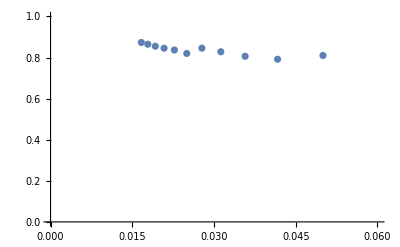

```mathematica
ListPlot[Transpose@{OneOverL,PercentageDelta0pt7},PlotRange->{{0,0.06},{0,1}}]
```

```mathematica
PercentageDelta0pt9 = {0.81,0.840278,0.836735,0.832031,0.845679,0.86,0.876033,0.881944,0.857988,0.866071,0.874444}
```

{0.81,0.840278,0.836735,0.832031,0.845679,0.86,0.876033,0.881944,0.857988,0.866071,0.874444}

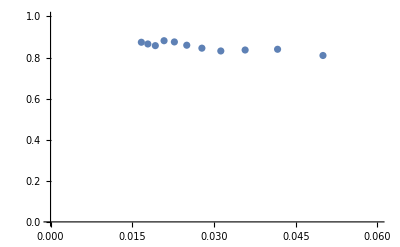

```mathematica
ListPlot[Transpose@{OneOverL,PercentageDelta0pt9},PlotRange->{{0,0.06},{0,1}}]
```